# CRM with abiotic resources

This notebook analyze the consumer resource model with abiotic resources, evaluating both the full solution and the quasi stationary approximation. I also check the analytical result with simulations, to asses wheter there is a combination of parameters that leads to the same results for the 2 solutions . I used the notation in which Nx represent the population  and Rx represent the resource abundancy.
Let’s break down the physical meaning of each parameter:

1. c:
   -  This parameter represents the dilution rate of the chemostat, which is the rate at which the contents of the reactor are removed or replaced. In practical terms, it corresponds to the flow rate of fresh medium into the chemostat.

2. μmax:
   -  This parameter represents the maximum specific growth rate of the microorganisms (e.g., bacteria) . It is a measure of how quickly the microorganisms can reproduce when resources are not limiting.

3. k_s:
   -  This is the half-saturation constant, and it represents the nutrient concentration at which the growth rate is half-maxima.

4. γ:
   - This parameter often represents the yield coefficient, describing the number of units of nutrient that are consumed to produce one bacterium (divided by the volume).

5. d:
   -  The parameter d represents the death or decay rate of the microorganisms.

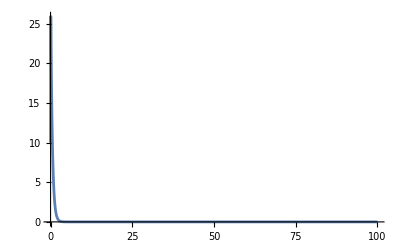

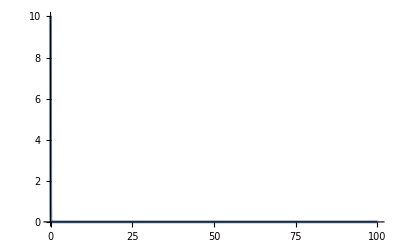

```mathematica
param = {c -> 2, μmax -> 3, ks -> 10, γ -> 2, d -> 2};
sol = NDSolve[{D[Rx[t], t] == (-c*Nx[t]*Rx[t] + μmax*Rx[t]/(ks + Rx[t])) /. param, D[Nx[t], t] == (Nx[t] (γ*c*Rx[t] - d)) /. param, Rx[0] == 10, Nx[0] == 10}, {Nx[t], Rx[t]}, {t, 0, 100}];
Plot[Evaluate[Nx[t] /. sol], {t, 0, 100}, PlotRange -> All]
Plot[Evaluate[Rx[t] /. sol], {t, 0, 100}, PlotRange -> All]
```

## Quasi stationary approximation for CRM with abiotic resources

```mathematica
eq1=D[Nx[t],t]==(Nx[t] *(γ*c*(μmax-c*Nx[t]*ks)/(c*Nx[t])-d));
eq2=Rcrm==(μmax-c*Nx[t]*ks)/(c*Nx[t]);
sol=DSolve[eq1,Nx[t],t]
```

{{Nx[t]→(ⅇ^(-d t-c ks t γ+t (d+c ks γ)) γ μmax)/(d+c ks γ)+ⅇ^(-d t-c ks t γ) C[1]}}

Once I found the solution of the CRM with abiotic resource in the quasi stationary approximation, I can evaluate it for different values of the parameters.

{c→2,μmax→3,ks→10,γ→2,d→2}

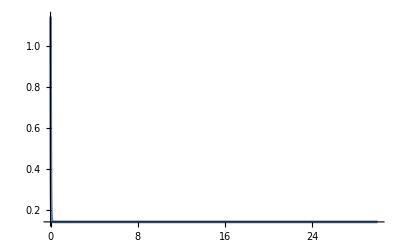

```mathematica
param = {c -> 2, μmax -> 3, ks -> 10, γ -> 2, d -> 2}
Plot[Evaluate[(ⅇ^(-d t-c ks t γ+t (d+c ks γ)) γ μmax)/(d+c ks γ)+ⅇ^(-d t-c ks t γ)/.param],{t,0,30},PlotRange->All]
```